```mathematica
Subscript[d, 1]=2
Subscript[d, 2]=2
Subscript[Σ, 1]=IdentityMatrix[d]
Subscript[Σ, 2]= IdentityMatrix[d]
Subscript[σ, 1]=0.01
Subscript[σ, 2]= 0.01
Subscript[β, 1]={{1.764052350,.40015721}}ᵀ
Subscript[β, 2]={{0.97873798,2.24089320}}ᵀ
Subscript[μ, 1]={{0.25987323,0.07116222}}ᵀ
Subscript[γ, 1]={{0.06725761,0.00170695}}ᵀ
Subscript[μ, 2]={{0.00184096,0.02913141}}ᵀ
Subscript[γ, 2]={{0.00358521,0.36544242}}ᵀ
```

2

2

{{1,0},{0,1}}

{{1,0},{0,1}}

0.01

0.01

{{1.76405},{0.400157}}

{{0.978738},{2.24089}}

{{0.259873},{0.0711622}}

{{0.0672576},{0.00170695}}

{{0.00184096},{0.0291314}}

{{0.00358521},{0.365442}}

```mathematica
Subscript[θ, 1PO]=Inverse[IdentityMatrix[Subscript[d, 1]]-Subscript[μ, 1].Subscript[γ, 1] ᵀ.Inverse[Subscript[μ, 2].Subscript[μ, 2] ᵀ+Subscript[Σ, 2]].Subscript[μ, 2].Subscript[γ, 2] ᵀ].Inverse[Subscript[μ, 1].Subscript[μ, 1] ᵀ+Subscript[Σ, 1]
].(Subscript[Σ, 1].Subscript[β, 1]-Subscript[μ, 1].Subscript[γ, 1] ᵀ.Inverse[Subscript[μ, 2].Subscript[μ, 2] ᵀ+Subscript[Σ, 2]].Subscript[Σ, 2].Subscript[β, 2])
Subscript[θ, 2PO]=Inverse[IdentityMatrix[Subscript[d, 2]]-Subscript[μ, 2].Subscript[γ, 2] ᵀ.Inverse[Subscript[μ, 1].Subscript[μ, 1] ᵀ+Subscript[Σ, 1]].Subscript[μ, 1].Subscript[γ, 1] ᵀ].Inverse[Subscript[μ, 2].Subscript[μ, 2] ᵀ+Subscript[Σ, 2]
].(Subscript[Σ, 2].Subscript[β, 2]-Subscript[μ, 2].Subscript[γ, 2] ᵀ.Inverse[Subscript[μ, 1].Subscript[μ, 1] ᵀ+Subscript[Σ, 1]].Subscript[Σ, 1].Subscript[β, 1])
```

{{1.62922},{0.363234}}

{{0.97836},{2.23491}}

```mathematica
PR1[t1_,t2_]:=0.5*(Subscript[β, 1] ᵀ.Subscript[Σ, 1].Subscript[β, 1]+Subscript[σ, 1]+(Subscript[μ, 1] ᵀ.t1+Subscript[γ, 1] ᵀ.t2)^2-2*(Subscript[β, 1] ᵀ.Subscript[Σ, 1].t1)+(t1ᵀ.Subscript[Σ, 1].t1))
PR2[t1_,t2_]:=0.5*(Subscript[β, 2] ᵀ.Subscript[Σ, 2].Subscript[β, 2]+Subscript[σ, 2]+(Subscript[μ, 2] ᵀ.t2+Subscript[γ, 2] ᵀ.t1)^2-2*(Subscript[β, 2] ᵀ.Subscript[Σ, 2].t2)+(t2ᵀ.Subscript[Σ, 2].t2))
```

```mathematica
SR[t1_,t2_]:=Flatten[PR1[t1,t2]+PR2[t1,t2]]
SR[Subscript[θ, 1PO],Subscript[θ, 2PO]]
Minimize[SR[{{t11,t12}}ᵀ,{{t21,t22}}ᵀ],{t11,t12,t21,t22}]
```

{0.175508}

{0.172438,{t11→1.63031,t12→0.297429,t21→0.943959,t22→2.23474}}

```mathematica
Subscript[θ, 1SO]={{1.630309922640284},{0.2974291516574217}}
Subscript[θ, 2SO]={{0.9439585846632687},{2.234735230121265}}
PR1[Subscript[θ, 1PO],Subscript[θ, 2PO]]
PR2[Subscript[θ, 1PO],Subscript[θ, 2PO]]
PR1[Subscript[θ, 1SO],Subscript[θ, 2SO]]
PR2[Subscript[θ, 1SO],Subscript[θ, 2SO]]
```

{{1.63031},{0.297429}}

{{0.943959},{2.23474}}

{{0.149377}}

{{0.0261309}}

{{0.150365}}

{{0.0220726}}

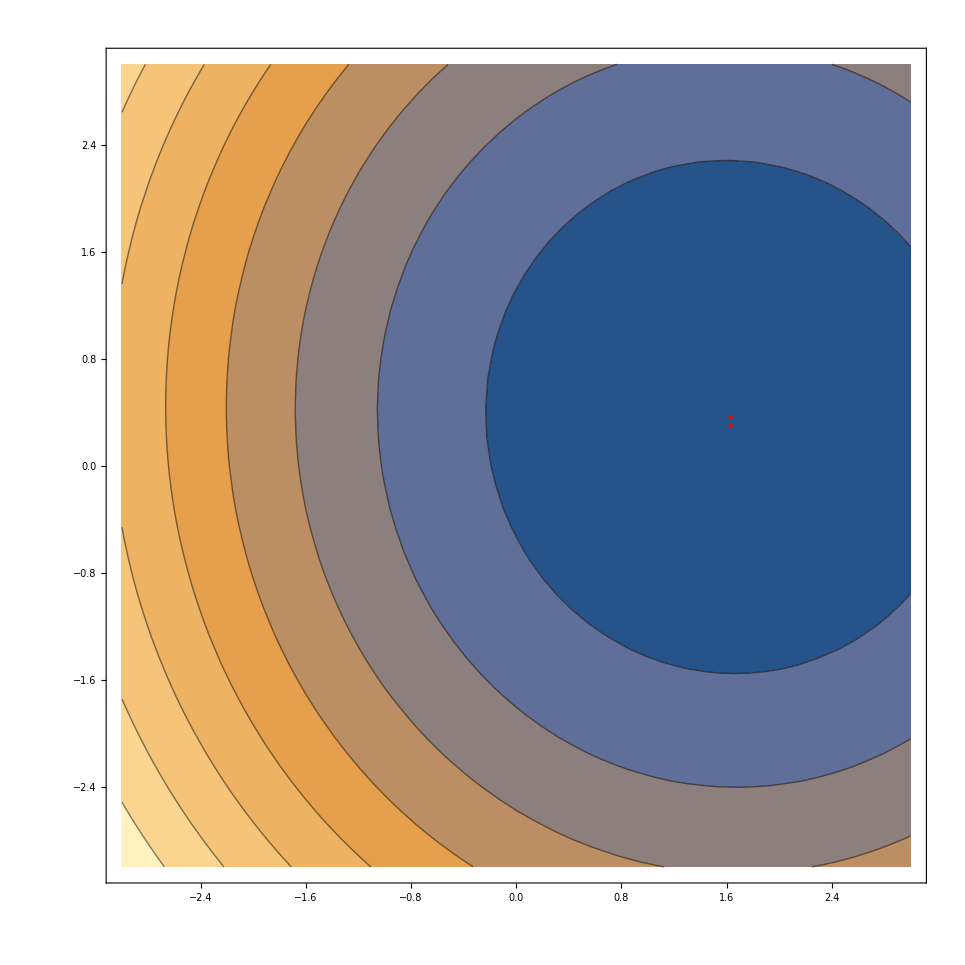

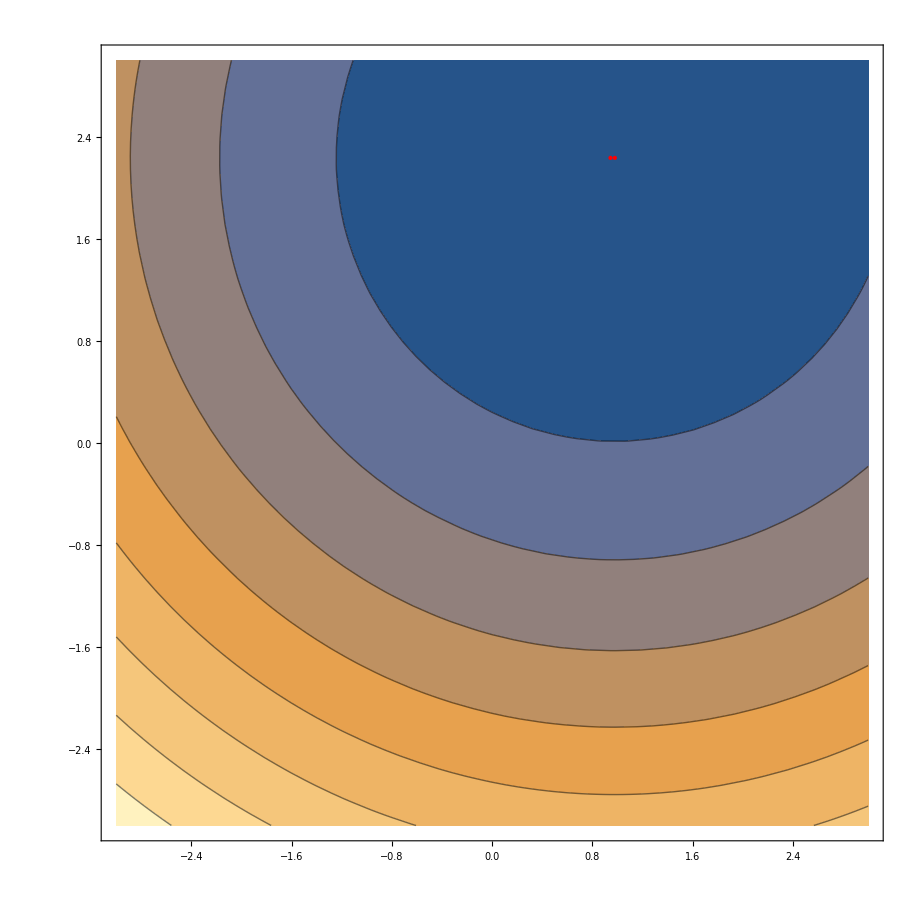

```mathematica
ContourPlot[PR1[{{t11},{t12}},Subscript[θ, 2PO]],{t11,-3,3},{t12,-3,3},
Epilog->{PointSize[Small],Red,Point[{{1.629216211797439,0.363234442192323},{1.630309922640284,0.2974291516574217}}]}]

ContourPlot[PR2[Subscript[θ, 1PO],{{t21},{t22}}],{t21,-3,3},{t22,-3,3},Epilog->{PointSize[Small],Red,Point[{{0.9783596849277038,2.234907046660419},{0.9439585846632687,2.234735230121265}}]}]
```